```mathematica
Get["NeutronBeam/NBeamIntegrand_fCorr.m"]
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
BinCenters[XYBinBoundaries_]:={Mean[#[[1]]],Mean[#[[2]]]}&/@XYBinBoundaries
```

```mathematica
IntegrationRules={"GaussBerntsenEspelidRule","GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule","CartesianRule","MultidimensionalRule"};
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
IntOptionList=Flatten[Table[
{strategy,Method->rule},
{strategy,IntegrationStrategies},{rule,IntegrationRules}],1]
```

{{GlobalAdaptive,Method→GaussBerntsenEspelidRule},{GlobalAdaptive,Method→GaussKronrodRule},{GlobalAdaptive,Method→LobattoKronrodRule},{GlobalAdaptive,Method→ClenshawCurtisRule},{GlobalAdaptive,Method→CartesianRule},{GlobalAdaptive,Method→MultidimensionalRule},{LocalAdaptive,Method→GaussBerntsenEspelidRule},{LocalAdaptive,Method→GaussKronrodRule},{LocalAdaptive,Method→LobattoKronrodRule},{LocalAdaptive,Method→ClenshawCurtisRule},{LocalAdaptive,Method→CartesianRule},{LocalAdaptive,Method→MultidimensionalRule}}

```mathematica
BRxBList={0.15,0.2,0.3,0.4,0.6,0.8,1.,1.2};
```

```mathematica
RoughDriftDistance=Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,BRxBList}],0.01]*0.8
```

{0.112,0.08,0.056,0.048,0.032,0.024,0.024,0.024}

```mathematica
XOffBRamp=-RoughDriftDistance/2
```

{-0.056,-0.04,-0.028,-0.024,-0.016,-0.012,-0.012,-0.012}

```mathematica
XY35BinsBRampXOff=Table[XYBinIntBoundaries[{-0.005,xmax-0.005,-xmax/2,7},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance}];
```

```mathematica
BinCentersBRampXOff=BinCenters[#]&/@XY35BinsBRampXOff;
```

### spectrum test

```mathematica
CloseKernels[]
```

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.220".

General::stop: Further output of LightweightGridClient`RemoteKernelClose::nokernel will be suppressed during this calculation.

{KernelObject[13,192.168.0.220,<defunct>],KernelObject[15,192.168.0.220,<defunct>],KernelObject[16,192.168.0.220,<defunct>],KernelObject[17,192.168.0.220,<defunct>],KernelObject[18,192.168.0.220,<defunct>],KernelObject[19,192.168.0.150,<defunct>],KernelObject[20,local,<defunct>],KernelObject[21,local,<defunct>],KernelObject[22,192.168.0.220,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[1,192.168.0.220],KernelObject[2,192.168.0.220],KernelObject[3,192.168.0.220],KernelObject[4,192.168.0.220],KernelObject[5,192.168.0.220],KernelObject[6,192.168.0.220],KernelObject[7,192.168.0.150],KernelObject[8,local],KernelObject[9,local]}

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35BinsDatafCorrXOff=ParallelMap[
(BinIntfCorr[0.,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.,1.5},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Wed 22 Apr 2020 11:33:00

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0960138 and 0.00011817 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.089109 and 0.000201407 for the integral and error estimates.

LinkObject::linkd: Unable to communicate with closed link LinkObject[59903@192.168.0.220,59904@192.168.0.220,331,11].

Kernels::rdead: Subkernel connected through KernelObject[3,192.168.0.220] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {12} assigned to KernelObject[3,192.168.0.220,<defunct>].

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.220".

OptionValue::nodef: Unknown option KernelSpeed for LightweightGridClient`RemoteKernelOpen.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[3,192.168.0.220,<defunct>] resurrected as KernelObject[10,192.168.0.220].

LinkObject::linkd: Unable to communicate with closed link LinkObject[49819@192.168.0.150,49820@192.168.0.150,411,15].

Kernels::rdead: Subkernel connected through KernelObject[7,192.168.0.150] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {16} assigned to KernelObject[7,192.168.0.150,<defunct>].

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.150".

LaunchKernels::clone: Kernel KernelObject[7,192.168.0.150,<defunct>] resurrected as KernelObject[11,192.168.0.150].

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200827 and 0.000243622 for the integral and error estimates.

LinkObject::linkd: Unable to communicate with closed link LinkObject[59893@192.168.0.220,59894@192.168.0.220,329,9].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[1,192.168.0.220] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {17} assigned to KernelObject[1,192.168.0.220,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.220".

General::stop: Further output of LightweightGridClient`RemoteKernelClose::nokernel will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[1,192.168.0.220,<defunct>] resurrected as KernelObject[12,192.168.0.220].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192089 and 0.000426871 for the integral and error estimates.

{{645.601,0.00966875},{171.343,0.0137703},{171.185,0.0134299},{172.324,0.0131011},{606.231,0.00882797},{7197.91,0.0960138},{233.23,0.142881},{285.913,0.140263},{403.538,0.136922},{7260.83,0.089109},{8217.,0.200827},{2910.21,0.309516},{210.136,0.314191},{729.161,0.301817},{9124.34,0.192089},{2088.53,0.205748},{1580.29,0.316522},{692.293,0.338865},{1712.9,0.317202},{16843.5,0.205666},{12012.8,0.122288},{2000.41,0.187982},{4998.31,0.208442},{2391.89,0.194655},{9636.3,0.130166},{1902.72,0.0400247},{2184.63,0.062267},{2119.86,0.0715124},{2413.34,0.0674549},{2108.79,0.0465285},{1933.75,0.00735444},{1909.36,0.0115582},{2476.53,0.0137562},{2161.88,0.0129143},{1690.57,0.0091012}}

5.23202

```mathematica
BinInt35BinsDatafCorrXOff={{645.600944375579,0.009668753830383525},{171.34286883836478,0.013770262147100979},{171.18519776773456,0.013429924393620287},{172.3240345798398,0.013101092939218283},{606.2313101021689,0.008827965714539067},{7197.914101537538,0.09601380964189567},{233.229868309272,0.14288117119656527},{285.913268,0.14026304316751928},{403.537534,0.13692243659018294},{7260.831264163388,0.08910902055030824},{8216.996773378092,0.2008267886564492},{2910.2052828314713,0.3095161671425572},{210.13577473909817,0.314190947705243},{729.16124,0.30181663781051027},{9124.340624,0.19208925611706984},{2088.5295718933535,0.20574830795992785},{1580.2926550562172,0.3165222728763739},{692.2931632058596,0.33886519665881737},{1712.903054,0.3172024222085471},{16843.53834829552,0.2056655154626358},{12012.826712,0.12228822220917841},{2000.4060782909746,0.1879818240535912},{4998.309974810663,0.20844167783235928},{2391.889980469602,0.19465517842660074},{9636.30221173415,0.13016642771930353},{1902.720884,0.04002474454563221},{2184.6309114100127,0.06226701183250828},{2119.8562582977024,0.07151239765348696},{2413.341636960444,0.0674549477304133},{2108.7882151628773,0.046528537098116954},{1933.754055,0.007354436267303929},{1909.3555170807574,0.011558183004477585},{2476.5288156776996,0.013756176992109959},{2161.877244123919,0.012914343972023994},{1690.5702741441658,0.009101204557434522}};
```

```mathematica
ListPlot3D[Transpose[{BinCentersBRampXOff[[2,All,1]],BinCentersBRampXOff[[2,All,2]],BinInt35BinsDatafCorrXOff[[All,2]]}],InterpolationOrder->0]
```

-Graphics3D-

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35BinsbvaryfCorrXOff1=ParallelMap[
(BinIntfCorr[0.,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.,0.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Wed 22 Apr 2020 17:52:02

LinkObject::linkd: Unable to communicate with closed link LinkObject[61478@192.168.0.220,61479@192.168.0.220,628,10].

Kernels::rdead: Subkernel connected through KernelObject[14,192.168.0.220] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {41} assigned to KernelObject[14,192.168.0.220,<defunct>].

LightweightGridClient`RemoteKernelClose::nokernel: Kernel could not be closed because no kernel was found for the given link "192.168.0.220".

OptionValue::nodef: Unknown option KernelSpeed for LightweightGridClient`RemoteKernelOpen.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[14,192.168.0.220,<defunct>] resurrected as KernelObject[22,192.168.0.220].

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0891125 and 0.000201447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200842 and 0.000247382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192103 and 0.000428453 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0960178 and 0.00011818 for the integral and error estimates.

{{644.198,0.00966887},{166.258,0.0137704},{166.112,0.0134301},{166.87,0.0131012},{618.115,0.00882806},{7111.59,0.0960178},{245.648,0.142887},{248.671,0.140269},{358.7,0.136928},{7621.55,0.0891125},{8540.74,0.200842},{2889.58,0.309538},{221.268,0.314215},{694.57,0.301836},{8969.83,0.192103},{2195.3,0.205755},{1570.49,0.316533},{687.611,0.338879},{1664.69,0.317214},{16330.3,0.205675},{10997.4,0.122281},{2203.38,0.187971},{4568.77,0.20843},{2307.18,0.194647},{12099.3,0.13016},{1724.98,0.0400127},{2099.5,0.0622493},{2107.09,0.0714921},{2292.49,0.0674373},{2041.21,0.0465161},{1734.81,0.00734895},{2208.28,0.0115482},{2229.67,0.0137466},{1858.69,0.0129054},{1593.38,0.00909479}}

4.90622

```mathematica
BinInt35BinsbvaryfCorrXOff1={{644.1978524261579,0.009668870808766309},{166.25796678549156,0.013770428497604193},{166.1124338828022,0.013430082448900234},{166.86957588752955,0.013101243203009861},{618.1150076735729,0.008828062997352514},{7111.588542508771,0.09601784580918898},{245.6484757944534,0.14288744221200628},{248.670564,0.14026919741530075},{358.699685,0.13692822807959343},{7621.552337809157,0.08911254730344553},{8540.744004860784,0.2008416686015681},{2889.576961252307,0.3095379454462416},{221.26819138362788,0.3142148370473309},{694.569991,0.3018358275727587},{8969.828693,0.19210333549227043},{2195.301230522043,0.2057547446685104},{1570.485583178707,0.3165329787318258},{687.6112635987773,0.3388789673984348},{1664.69429,0.317214473880038},{16330.319795829068,0.20567506583024345},{10997.384009069701,0.12228133380542719},{2203.376933,0.18797064923373583},{4568.769452532101,0.2084297726434307},{2307.184514139649,0.19464655610513376},{12099.298286,0.13016048391969526},{1724.9779468188035,0.040012653056899834},{2099.502128839032,0.06224929416147005},{2107.0909359501397,0.07149212052897251},{2292.489432476408,0.06743730644847466},{2041.2052821898683,0.046516124707213224},{1734.808969739432,0.0073489458715007725},{2208.281022,0.011548198845520389},{2229.669943811605,0.013746630279883636},{1858.6908188523516,0.012905381960191394},{1593.3819495238022,0.009094794722205646}};
```

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35BinsbvaryfCorrXOff2=ParallelMap[
(BinIntfCorr[0.001,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.,0.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Wed 22 Apr 2020 23:01:50

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0891313 and 0.000201488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0960374 and 0.000118209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200856 and 0.000247409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192118 and 0.000428512 for the integral and error estimates.

{{556.889,0.00967181},{148.225,0.0137746},{165.83,0.0134342},{162.902,0.0131052},{609.411,0.00883077},{7602.95,0.0960374},{259.819,0.142916},{233.137,0.140298},{407.646,0.136957},{6504.43,0.0891313},{8316.3,0.200856},{2831.33,0.30956},{233.74,0.314237},{644.806,0.301858},{8482.21,0.192118},{2371.35,0.205746},{1290.92,0.31652},{691.077,0.338865},{1559.12,0.317203},{15960.7,0.205668},{9183.66,0.122266},{2080.06,0.187948},{5010.78,0.208405},{2258.67,0.194624},{9646.6,0.130145},{1690.28,0.0400059},{1780.,0.0622389},{2360.79,0.0714802},{2326.48,0.0674261},{2079.48,0.0465084},{1472.33,0.00734751},{1788.28,0.011546},{2615.23,0.013744},{1702.7,0.0129029},{1501.9,0.00909304}}

4.7949

```mathematica
BinInt35BinsbvaryfCorrXOff2={{556.8892828242712,0.009671806440617875},{148.2252883720971,0.013774615963581975},{165.82964298214125,0.01343417630877913},{162.90162175271712,0.013105246202838155},{609.4110134053727,0.008830766698589204},{7602.948507995841,0.09603737468430018},{259.818856319953,0.1429164963345679},{233.13715652882746,0.14029795174733867},{407.645629,0.1369565769477488},{6504.43106262316,0.0891312579916066},{8316.296788478572,0.20085550965621243},{2831.327423831068,0.3095597094926186},{233.73968291242446,0.31423724134608944},{644.8059260556727,0.301858486601238},{8482.205077,0.19211827895801364},{2371.3509415392036,0.20574567901970595},{1290.9213038092207,0.31651980896184284},{691.0769406223503,0.33886491728570833},{1559.1196073506112,0.31720255415565773},{15960.731541587389,0.20566756683891574},{9183.660959279414,0.12226643953992698},{2080.060025991416,0.18794820265206863},{5010.775306101695,0.20840512209300283},{2258.6670593288877,0.19462391077410313},{9646.597953986018,0.13014537163090678},{1690.2785717104193,0.04000590101421321},{1780.0020664073356,0.062238880515918346},{2360.7942671315736,0.07148024945391379},{2326.484550955141,0.06742613771021293},{2079.483646933786,0.046508410339944836},{1472.3314852269848,0.0073475064925780575},{1788.2803248959076,0.011545953047565609},{2615.232415,0.013743964899518839},{1702.698896086627,0.012902890202763511},{1501.8996186600293,0.009093035327605588}};
```

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35BinsbvaryfCorrXOff3=ParallelMap[
(BinIntfCorr[-0.001,#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.,0.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Thu 23 Apr 2020 19:38:35

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0959983 and 0.000118151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0890938 and 0.000201407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200828 and 0.000246812 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192088 and 0.000428393 for the integral and error estimates.

{{644.52,0.00966593},{164.257,0.0137662},{172.943,0.013426},{171.453,0.0130972},{587.458,0.00882536},{7390.12,0.0959983},{250.034,0.142858},{249.169,0.14024},{360.414,0.1369},{7481.4,0.0890938},{8785.34,0.200828},{2947.45,0.309516},{252.173,0.314192},{636.324,0.301813},{8692.14,0.192088},{2500.53,0.205765},{1493.93,0.316546},{631.151,0.338893},{1537.6,0.317226},{17627.,0.205683},{10488.8,0.122296},{2047.42,0.187993},{5260.87,0.208454},{2350.59,0.194669},{9788.08,0.130176},{1763.1,0.0400194},{2152.87,0.0622597},{2367.81,0.071504},{2244.17,0.0674485},{2185.38,0.0465238},{1763.37,0.00735039},{1979.64,0.0115504},{2410.27,0.0137493},{1838.54,0.0129079},{1701.27,0.00909656}}

5.25103

```mathematica
bList={0.,0.001,-0.001};
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 3. Some property values cannot be computed.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::dof: The number of parameters 3 is not less than the number of data values 3. Some property values cannot be computed.

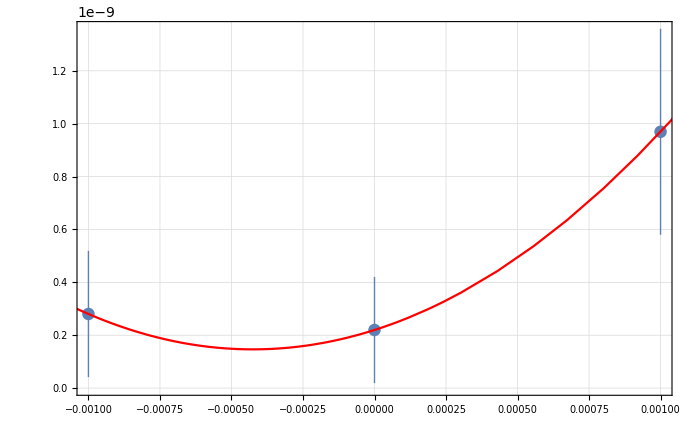
{b0 =  | -0.000425258
FittedModel[1.46539×10^-10+0.000405081 (0.000425258+b)^2] | 
Missing[] | 
Missing[] | ,-Graphics-}

```mathematica
fCorrfit=Chi2FitandPlot[BinInt35BinsDatafCorrXOff[[All,2]]/Total[BinInt35BinsDatafCorrXOff[[All,2]]],{BinInt35BinsbvaryfCorrXOff1/Total[BinInt35BinsbvaryfCorrXOff1[[All,2]]],BinInt35BinsbvaryfCorrXOff2/Total[BinInt35BinsbvaryfCorrXOff2[[All,2]]],BinInt35BinsbvaryfCorrXOff3/Total[BinInt35BinsbvaryfCorrXOff3[[All,2]]]},bList,4]
```

```mathematica
Print[DateString[]]
t0=AbsoluteTime[];
BinInt35BinsbvaryfCorrXOff4=ParallelMap[
(BinIntfCorr[fCorrfit[[1,1,1,2]],#,{Pi,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.,0.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,XOffBRamp[[2]],0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]//AbsoluteTiming
)&,XY35BinsBRampXOff[[2]],Method->"FinestGrained"]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Fri 24 Apr 2020 00:53:40

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,-0.0163118}. NIntegrate obtained 0.0960095 and 0.000118168 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0239243,0.0176882}. NIntegrate obtained 0.0891046 and 0.00020143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,0.0196882}. NIntegrate obtained 0.192097 and 0.000428427 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in yD near {xD,yD} = {-0.0124957,-0.0163118}. NIntegrate obtained 0.200836 and 0.000246824 for the integral and error estimates.

{{565.303,0.00966762},{168.156,0.0137686},{174.429,0.0134283},{175.006,0.0130995},{586.905,0.00882691},{7446.05,0.0960095},{250.895,0.142875},{252.169,0.140257},{362.691,0.136916},{7539.53,0.0891046},{8890.85,0.200836},{2938.39,0.309529},{224.411,0.314205},{694.478,0.301826},{8701.44,0.192097},{2288.55,0.205759},{1342.16,0.316539},{656.913,0.338885},{1659.12,0.31722},{15679.5,0.205678},{9589.04,0.122288},{2206.41,0.18798},{4828.04,0.20844},{2347.32,0.194656},{11255.6,0.130167},{1760.33,0.0400155},{2155.02,0.0622537},{2385.57,0.0714972},{2222.7,0.0674421},{2043.91,0.0465194},{1840.48,0.00734956},{1902.16,0.0115492},{2386.93,0.0137478},{1737.41,0.0129064},{1642.97,0.00909554}}

4.70098

```mathematica
bList={0.,0.001,-0.001,fCorrfit[[1,1,1,2]]};
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

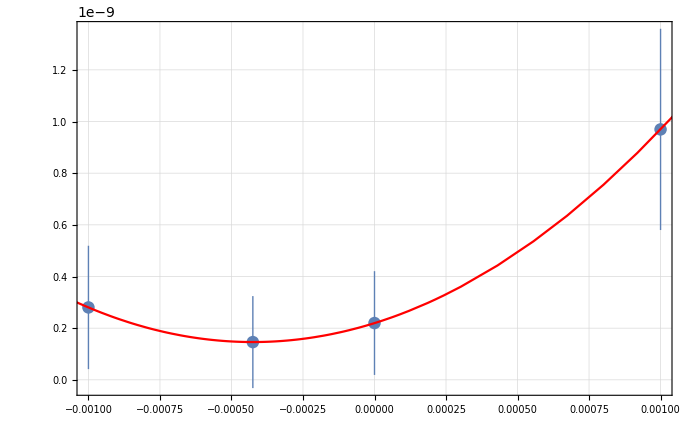
{b0 =  | -0.000425103
FittedModel[1.46267×10^-10+0.000405392 (0.000425103+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000425103 | 0.000342388 | -1.24158 | 0.431654
scale | 0.000405392 | 0.000274615 | 1.47622 | 0.379043
yoffset | 1.46267×10^-10 | 1.28609×10^-10 | 1.1373 | 0.45916 | 
 | DF | SS | MS
Model | 3 | 9.44203 | 3.14734
Error | 1 | 2.90329×10^-6 | 2.90329×10^-6
Uncorrected Total | 4 | 9.44203 | 
Corrected Total | 3 | 3.77118 |  | ,-Graphics-}

```mathematica
fCorrfit2=Chi2FitandPlot[BinInt35BinsDatafCorrXOff[[All,2]]/Total[BinInt35BinsDatafCorrXOff[[All,2]]],{BinInt35BinsbvaryfCorrXOff1/Total[BinInt35BinsbvaryfCorrXOff1[[All,2]]],BinInt35BinsbvaryfCorrXOff2/Total[BinInt35BinsbvaryfCorrXOff2[[All,2]]],BinInt35BinsbvaryfCorrXOff3/Total[BinInt35BinsbvaryfCorrXOff3[[All,2]]],BinInt35BinsbvaryfCorrXOff4/Total[BinInt35BinsbvaryfCorrXOff4[[All,2]]]},bList,4]
```

```mathematica
fCorrfit2[[1,1,1,2]]
```

-0.000425103